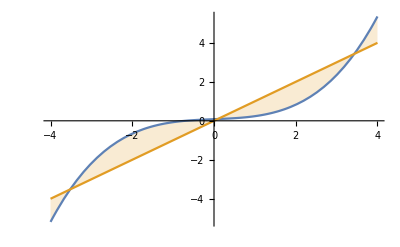

```mathematica
f[x_]:=x^3 + Sin[x] - 12x + 1 ;

ϕ[x_]:=(x^3 + Sin[x] + 1)/12;
Plot[{ϕ[x],x},{x,-4,4},Filling->{2->{1}}]
```

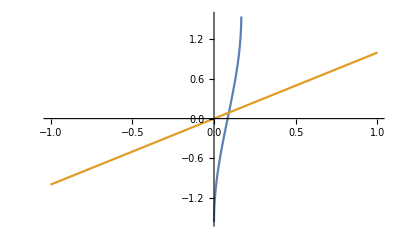

-Graphics-

```mathematica
ϕ[x_]:=ArcSin[12x-1-x^3];
Plot[{ϕ[x],x},{x,-1,1}]
```

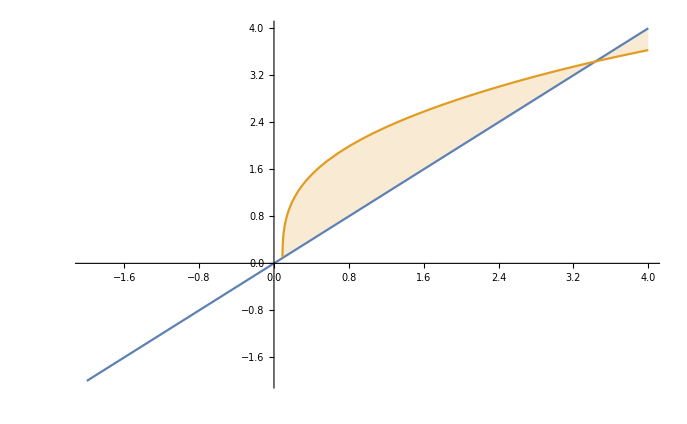

```mathematica
ϕ[x_]:=Power[12x - 1 - Sin[x],1/3];
Plot[{x,ϕ[x]},{x,-2,4},Filling->{2->{1}}]
```

```mathematica
FindRoot[x-(-1+12 x-Sin[x])^(1/3)==0,{x,0}]
```

{x→0.0909661-7.25268×10^-15 ⅈ}

```mathematica
Subscript[x, 0]=0.09096612060016304-7.25268130113225*^-15 ⅈ;
Subscript[x, n+1]=ϕ[Subscript[x, 0]];
ϵ=0.5*10^-4;
```

```mathematica
While[Abs[Subscript[x, n+1]-Subscript[x, 0]]>ϵ,
Subscript[x, n+1]=ϕ[Subscript[x, n+1]];
];
```

```mathematica
Print[Subscript[x, n+1]];
Print[Subscript[x, 0]];
```

0.0909661-3.21495×10^-12 ⅈ

0.0909661-7.25268×10^-15 ⅈ